## Seasonal Ricker model - EWS in rb - Singles

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=0.2;
bh=1.8;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="trans_rb_skewtrial";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

5

```mathematica
(* Realisation number to display *)
displayNum=1;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
realNum=1;
seriesB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Non-breeding",_,_}][[;;,{3,4}]];
seriesTotal= Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Total",_,_}][[;;,{3,4}]];
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[dfEws[[;;,1]]][[1]];
stateVals=Union[dfEws[[2;;,2]]];
```

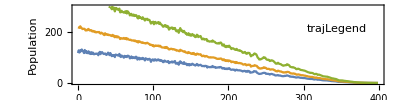

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB,seriesTotal},
Joined->True,
LabelStyle->12,
PlotLegends->Placed[trajLegend,Scaled[{0.85,0.7}]],
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},{0,300}}]
```

```mathematica
(* line legend *)
trajLegend=LineLegend[TMBcolours[[1;;3]],{"Breeding","Non-breeding","Total"},Spacings->{0,0.2},LabelStyle->10]
```

### Output

```mathematica
rTicks=Range[bl,bh,0.5];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

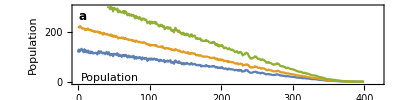

```mathematica
plotTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,300}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots (Mean +/- SD)

### Variance

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

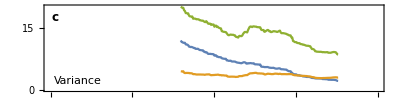

```mathematica
(* Plot EWS *)
plotVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

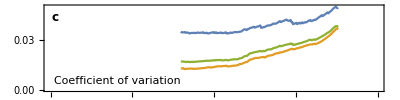

```mathematica
(* Plot EWS *)
plotCv=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

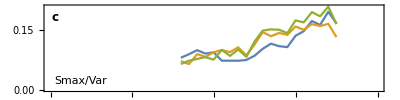

```mathematica
(* Plot EWS *)
plotSmaxVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax/Var",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

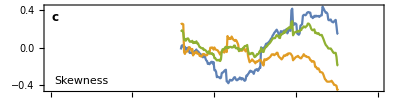

```mathematica
(* Plot EWS *)
plotSkew=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

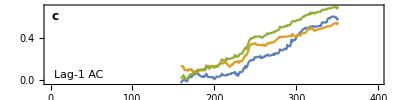

```mathematica
(* Plot EWS *)
plotAc1=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-1 AC",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

10

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.985751 | -0.972582 | -0.966645 | -0.973338 | -0.982297 | -0.977332 | -0.972042 | -0.984348 | -0.978303 | -0.983916 | -0.983808 | -0.984996 | -0.982729 | -0.979491 | -0.983484 | -0.979383 | -0.986399 | -0.984024 | -0.975173 | -0.988126 | -0.981002 | -0.974849 | -0.989961 | -0.977332 | -0.977871 | -0.991149 | -0.988018 | -0.981326 | -0.981973 | -0.981218 | -0.972798 | -0.978843 | -0.983808 | -0.984348 | -0.986183 | -0.988018 | -0.989961 | -0.983592 | -0.982837 | -0.986075 | -0.984996 | -0.98845 | -0.977763 | -0.991472 | -0.98057 | -0.981218 | -0.985535 | -0.984672 | -0.981649 | -0.987586 | -0.984672 | -0.979814 | -0.968264 | -0.988882 | -0.985535 | -0.973122 | -0.971287 | -0.983916 | -0.971395 | -0.985751 | -0.966429 | -0.963083 | -0.964486 | -0.983053 | -0.9837 | -0.981865 | -0.975928 | -0.978195 | -0.977332 | -0.991472 | -0.975281 | -0.981326 | -0.965458 | -0.971179 | -0.98737 | -0.988666 | -0.991796 | -0.988558 | -0.983269 | -0.971718 | -0.970207 | -0.988774 | -0.983808 | -0.984672 | -0.986831 | -0.983269 | -0.983053 | -0.977871 | -0.969775 | -0.981434 | -0.976684 | -0.979383 | -0.981326 | -0.985427 | -0.976576 | -0.982081 | -0.981434 | -0.988558 | -0.978627 | -0.966429
Non-breeding | -0.428433 | -0.76522 | -0.926598 | -0.658031 | -0.588839 | -0.821891 | -0.851684 | -0.897992 | -0.901015 | -0.902094 | -0.955203 | -0.358161 | -0.927353 | -0.915911 | -0.825885 | -0.528605 | -0.915911 | -0.86766 | -0.912349 | -0.621546 | -0.869387 | -0.677461 | -0.955095 | -0.803649 | -0.942789 | -0.878346 | -0.931779 | -0.884067 | -0.900475 | -0.644754 | -0.79307 | -0.718048 | -0.877915 | -0.959953 | -0.785622 | -0.854059 | -0.802677 | -0.847474 | -0.836788 | -0.771049 | -0.842185 | -0.907815 | -0.799223 | -0.909434 | -0.85611 | -0.907275 | -0.835384 | -0.890112 | -0.634067 | -0.890544 | -0.765976 | -0.827504 | -0.750648 | -0.93329 | -0.932427 | -0.891731 | -0.733377 | -0.842725 | -0.899935 | -0.949158 | -0.738234 | -0.0739421 | -0.640004 | -0.882232 | -0.925842 | -0.861399 | -0.911377 | -0.621438 | -0.698294 | -0.924439 | -0.693005 | -0.40544 | -0.845747 | -0.928864 | -0.936744 | -0.946351 | -0.92282 | -0.953584 | -0.87133 | -0.672712 | -0.376511 | -0.914508 | -0.821999 | -0.916451 | -0.87446 | -0.786809 | -0.881153 | -0.330203 | -0.782383 | -0.00539724 | -0.90706 | -0.744711 | -0.722474 | -0.870035 | -0.769646 | -0.786054 | -0.941818 | -0.923683 | -0.935341 | -0.52677
Total | -0.786917 | -0.927461 | -0.958441 | -0.901446 | -0.917422 | -0.922927 | -0.93329 | -0.944301 | -0.902418 | -0.95639 | -0.873813 | -0.911485 | -0.909111 | -0.957578 | -0.864961 | -0.904577 | -0.948402 | -0.939767 | -0.960168 | -0.936528 | -0.927569 | -0.802461 | -0.982081 | -0.930484 | -0.939443 | -0.968048 | -0.957146 | -0.890328 | -0.947539 | -0.876079 | -0.908463 | -0.903929 | -0.963299 | -0.967832 | -0.933938 | -0.970855 | -0.966537 | -0.925302 | -0.919905 | -0.954879 | -0.908247 | -0.965674 | -0.874136 | -0.97323 | -0.944193 | -0.960384 | -0.900367 | -0.957794 | -0.950237 | -0.945272 | -0.899935 | -0.94959 | -0.846826 | -0.966213 | -0.971826 | -0.946891 | -0.892811 | -0.912673 | -0.950993 | -0.964702 | -0.908787 | -0.641623 | -0.85924 | -0.950885 | -0.948294 | -0.933614 | -0.967185 | -0.917422 | -0.84035 | -0.968804 | -0.904793 | -0.857405 | -0.92228 | -0.910622 | -0.977116 | -0.976468 | -0.971179 | -0.972042 | -0.936744 | -0.928001 | -0.876295 | -0.978951 | -0.936313 | -0.955527 | -0.935233 | -0.948726 | -0.935449 | -0.807103 | -0.905548 | -0.903929 | -0.939767 | -0.911269 | -0.902202 | -0.948187 | -0.913968 | -0.939227 | -0.942034 | -0.958441 | -0.961356 | -0.856649

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

12

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.490177 | 0.337651 | 0.496438 | 0.352979 | -0.145078 | -0.237263 | 0.700453 | 0.117768 | -0.169365 | -0.0668178 | -0.0633636 | 0.251835 | 0.719775 | 0.315091 | 0.458873 | 0.166451 | 0.42595 | 0.44959 | 0.39497 | 0.0486831 | -0.194408 | 0.65177 | 0.347582 | 0.644106 | 0.228519 | 0.0601252 | 0.16753 | 0.692681 | -0.278174 | -0.515868 | 0.577828 | -0.529793 | 0.748705 | -0.261658 | 0.00906736 | 0.57513 | 0.415911 | 0.480894 | -0.838083 | 0.267595 | -0.269214 | 0.481541 | -0.072215 | -0.0574266 | 0.230354 | 0.710384 | -0.27256 | -0.0420984 | 0.266084 | -0.0790155 | -0.224201 | 0.335816 | 0.700561 | 0.399288 | 0.580959 | -0.0248273 | -0.087975 | 0.341321 | -0.588839 | 0.484888 | 0.292854 | 0.384067 | 0.550518 | 0.668502 | 0.572215 | -0.632124 | -0.118415 | 0.545877 | 0.591537 | -0.203368 | 0.0737263 | -0.240609 | 0.0700561 | 0.402202 | -0.0659542 | 0.183398 | 0.787025 | -0.260687 | -0.246762 | -0.759715 | -0.798143 | -0.356865 | -0.109132 | 0.0749136 | 0.273532 | -0.776015 | 0.677353 | 0.483808 | -0.165263 | 0.471395 | 0.490177 | -0.254642 | -0.414832 | 0.365501 | 0.128886 | -0.36658 | -0.266947 | 0.0495466 | 0.370035 | 0.400907
Non-breeding | -0.547712 | -0.0558074 | -0.0786917 | -0.704987 | -0.409326 | 0.261982 | -0.631045 | -0.403605 | -0.0355138 | -0.23845 | -0.197107 | 0.617876 | 0.580527 | 0.333873 | 0.568437 | -0.377375 | 0.287673 | -0.122841 | -0.134931 | -0.374028 | -0.696244 | 0.397776 | 0.320704 | -0.25313 | 0.215889 | -0.173143 | 0.524935 | -0.399935 | -0.551598 | -0.724741 | 0.558938 | -0.341213 | 0.540371 | -0.137845 | 0.106326 | -0.191818 | -0.403713 | 0.445488 | 0.67487 | 0.0494387 | -0.168718 | 0.297388 | -0.721179 | -0.565954 | 0.388601 | 0.16019 | -0.431779 | 0.575885 | -0.521589 | -0.321244 | 0.518566 | 0.540587 | -0.226144 | -0.0881908 | 0.0789076 | -0.352116 | -0.185665 | 0.512522 | -0.33668 | -0.268243 | -0.138709 | 0.415047 | -0.0388601 | 0.775799 | 0.5462 | -0.282275 | -0.634175 | 0.76155 | -0.309478 | 0.712111 | 0.169257 | -0.615825 | 0.167746 | 0.507556 | -0.346395 | -0.127915 | -0.530225 | 0.435989 | -0.308938 | -0.465889 | -0.165155 | -0.626403 | -0.163644 | 0.162025 | 0.587327 | -0.696028 | -0.0142487 | -0.171848 | 0.194301 | -0.47269 | 0.483808 | 0.463839 | -0.763817 | 0.609348 | -0.359564 | 0.671848 | 0.375972 | 0.292746 | -0.397345 | -0.525043
Total | 0.218264 | 0.0653066 | 0.367444 | 0.202073 | -0.254426 | -0.448942 | -0.115717 | 0.277202 | -0.502267 | -0.33139 | -0.194085 | -0.0705959 | 0.496978 | 0.212327 | 0.638601 | -0.282383 | 0.364529 | -0.503238 | 0.360535 | -0.148424 | -0.607837 | 0.569408 | 0.058506 | 0.279253 | -0.099525 | -0.333873 | 0.0359456 | -0.259823 | -0.102332 | -0.820812 | 0.794473 | -0.723446 | 0.714918 | -0.0759931 | 0.187716 | 0.429728 | 0.309154 | 0.524072 | -0.756261 | 0.513817 | -0.474525 | 0.44851 | -0.615717 | -0.0500864 | 0.0532168 | 0.537781 | -0.443437 | 0.558506 | 0.246546 | -0.243415 | 0.0556995 | 0.298035 | 0.1875 | 0.461248 | 0.453692 | -0.249136 | -0.395078 | 0.412025 | -0.633851 | 0.147129 | -0.235212 | 0.231541 | 0.748597 | 0.568113 | 0.521913 | -0.638709 | -0.59035 | 0.705959 | 0.545337 | 0.0438256 | -0.564443 | -0.247085 | 0.0533247 | 0.471179 | -0.0185665 | -0.110212 | 0.399719 | -0.388061 | -0.55095 | -0.790695 | -0.787673 | -0.655656 | -0.346287 | -0.0406952 | 0.552785 | -0.422496 | 0.699914 | -0.427137 | -0.715889 | 0.557103 | 0.501727 | -0.538536 | -0.699806 | 0.591537 | -0.100065 | 0.0845207 | -0.34715 | -0.000539724 | 0.158787 | -0.0309801

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

6

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.804728 | 0.64756 | 0.652202 | 0.626079 | 0.713946 | 0.376079 | 0.807427 | -0.0457686 | 0.606865 | 0.378994 | 0.772345 | 0.731002 | 0.827504 | 0.874244 | 0.354598 | 0.672927 | 0.744387 | 0.883636 | 0.663644 | 0.16332 | 0.794365 | 0.769106 | 0.748057 | 0.19592 | 0.747193 | 0.770402 | 0.65285 | 0.809909 | 0.864313 | 0.659326 | 0.886334 | 0.762953 | 0.692789 | 0.46114 | 0.640976 | 0.611615 | -0.102979 | 0.768135 | 0.903389 | 0.715134 | 0.121114 | 0.535622 | 0.87975 | 0.449482 | 0.161377 | 0.62867 | 0.721287 | 0.502159 | 0.887306 | 0.0862478 | 0.753346 | 0.64756 | 0.900151 | -0.28152 | 0.724957 | 0.669905 | 0.717185 | 0.282491 | 0.867444 | 0.560233 | 0.868092 | 0.883528 | 0.731434 | 0.567681 | 0.744819 | 0.477332 | 0.412781 | 0.842401 | 0.647668 | 0.200022 | 0.919905 | 0.709845 | 0.604598 | 0.914292 | 0.52677 | -0.108161 | 0.171524 | 0.155117 | 0.693869 | 0.738018 | 0.558614 | -0.236075 | 0.929188 | 0.771265 | 0.820596 | 0.812284 | 0.619063 | 0.848014 | 0.874892 | 0.803325 | 0.818437 | 0.857621 | 0.297496 | 0.471611 | 0.866256 | 0.813472 | 0.00518135 | 0.80829 | 0.394214 | 0.792962
Non-breeding | 0.974309 | 0.969775 | 0.967077 | 0.903282 | 0.911917 | 0.93804 | 0.930807 | 0.965782 | 0.972258 | 0.941602 | 0.955743 | 0.965242 | 0.99158 | 0.97269 | 0.92228 | 0.926706 | 0.877807 | 0.960492 | 0.969344 | 0.866364 | 0.919689 | 0.979814 | 0.958333 | 0.930052 | 0.98532 | 0.970639 | 0.946783 | 0.940091 | 0.954016 | 0.973014 | 0.985427 | 0.960492 | 0.989421 | 0.967725 | 0.978951 | 0.929404 | 0.96427 | 0.973338 | 0.978627 | 0.870142 | 0.905009 | 0.896157 | 0.970747 | 0.961464 | 0.800194 | 0.895617 | 0.970963 | 0.941386 | 0.978519 | 0.909326 | 0.957686 | 0.965026 | 0.983592 | 0.773424 | 0.957902 | 0.96114 | 0.94171 | 0.988126 | 0.965134 | 0.804944 | 0.98899 | 0.956822 | 0.951533 | 0.984996 | 0.970423 | 0.820272 | 0.972474 | 0.941062 | 0.903497 | 0.967077 | 0.961896 | 0.884067 | 0.791775 | 0.958873 | 0.971071 | 0.943005 | 0.9538 | 0.972582 | 0.950993 | 0.959845 | 0.955311 | 0.952936 | 0.969668 | 0.916451 | 0.964162 | 0.968588 | 0.975497 | 0.954231 | 0.911269 | 0.983053 | 0.9769 | 0.935989 | 0.919581 | 0.954016 | 0.922712 | 0.939227 | 0.856218 | 0.952828 | 0.901554 | 0.988018
Total | 0.96535 | 0.939551 | 0.909542 | 0.839594 | 0.898856 | 0.951209 | 0.912889 | 0.906088 | 0.897345 | 0.920877 | 0.927893 | 0.957902 | 0.950669 | 0.972906 | 0.69484 | 0.877915 | 0.87079 | 0.976576 | 0.867012 | 0.728843 | 0.948402 | 0.945704 | 0.943653 | 0.601252 | 0.968804 | 0.962543 | 0.863666 | 0.969236 | 0.920121 | 0.911377 | 0.977655 | 0.909326 | 0.967617 | 0.919257 | 0.943113 | 0.901123 | 0.860643 | 0.92595 | 0.974525 | 0.869819 | 0.750648 | 0.819732 | 0.931995 | 0.910298 | 0.505073 | 0.941386 | 0.9375 | 0.888817 | 0.983377 | 0.918286 | 0.901123 | 0.954339 | 0.982945 | 0.680592 | 0.950993 | 0.955635 | 0.878886 | 0.834413 | 0.96481 | 0.815199 | 0.979598 | 0.96481 | 0.957686 | 0.888385 | 0.914832 | 0.914508 | 0.967077 | 0.933938 | 0.800518 | 0.94592 | 0.970207 | 0.926382 | 0.773748 | 0.943005 | 0.949266 | 0.572971 | 0.740393 | 0.873921 | 0.897021 | 0.922496 | 0.951533 | 0.905548 | 0.975173 | 0.91332 | 0.965997 | 0.951101 | 0.925842 | 0.947755 | 0.951857 | 0.976684 | 0.966537 | 0.931779 | 0.760579 | 0.881045 | 0.917206 | 0.930376 | 0.627699 | 0.932103 | 0.812824 | 0.96114

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

13

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.631579 | -0.621053 | -0.894737 | -0.842105 | -0.631579 | -0.821053 | -0.842105 | -0.852632 | -0.842105 | -0.915789 | -0.821053 | -0.8 | -0.736842 | -0.663158 | -0.6 | -0.810526 | -0.757895 | -0.873684 | -0.726316 | -0.842105 | -0.684211 | -0.915789 | -0.936842 | -0.915789 | -0.789474 | -0.747368 | -0.863158 | -0.852632 | -0.652632 | -0.747368 | -0.852632 | -0.831579 | -0.831579 | -0.905263 | -0.821053 | -0.894737 | -0.863158 | -0.821053 | -0.652632 | -0.894737 | -0.894737 | -0.926316 | -0.357895 | -0.915789 | -0.757895 | -0.810526 | -0.694737 | -0.894737 | -0.715789 | -0.905263 | -0.536842 | -0.894737 | -0.463158 | -0.810526 | -0.884211 | -0.905263 | -0.778947 | -0.884211 | -0.726316 | -0.968421 | -0.431579 | 0.210526 | -0.894737 | -0.936842 | -0.936842 | -0.842105 | -0.842105 | -0.747368 | -0.473684 | -0.905263 | -0.673684 | -0.757895 | -0.673684 | -0.589474 | -0.884211 | -0.852632 | -0.821053 | -0.873684 | -0.789474 | -0.736842 | -0.210526 | -0.905263 | -0.842105 | -0.526316 | -0.8 | -0.747368 | -0.863158 | -0.789474 | -0.589474 | -0.494737 | -0.810526 | -0.378947 | -0.873684 | -0.736842 | -0.947368 | -0.863158 | -0.926316 | -0.852632 | -0.884211 | -0.831579
Non-breeding | 0.410526 | 0.452632 | -0.557895 | 0.231579 | 0.505263 | 0.2 | 0.136842 | -0.231579 | 0.452632 | -0.0631579 | -0.242105 | 0.757895 | 0.484211 | 0.778947 | 0.242105 | 0.157895 | -0.252632 | -0.242105 | -0.178947 | 0.210526 | 0.4 | 0.284211 | -0.694737 | -0.0526316 | 0.210526 | 0.442105 | -0.842105 | 0.410526 | 0.0105263 | 0.821053 | 0.747368 | 0.536842 | 0.536842 | -0.652632 | 0.463158 | -0.557895 | 0.347368 | -0.378947 | 0.526316 | 0.105263 | 0.252632 | -0.210526 | 0.4 | -0.357895 | -0.115789 | 0.442105 | -0.0421053 | 0.0421053 | 0.442105 | -0.421053 | -0.157895 | -0.168421 | 0.410526 | -0.0842105 | 0.2 | -0.6 | 0.0736842 | -0.0631579 | 0.389474 | -0.873684 | 0.515789 | 0.705263 | 0.526316 | -0.389474 | -0.747368 | -0.421053 | 0.0421053 | 0.294737 | 0.357895 | -0.0210526 | 0.389474 | 0.463158 | 0.157895 | 0.336842 | -0.242105 | -0.221053 | -0.242105 | -0.536842 | -0.568421 | 0.242105 | 0.610526 | 0.463158 | 0.431579 | 0.242105 | -0.463158 | 0.4 | 0.2 | 0.821053 | 0.368421 | 0.705263 | 0.273684 | 0.494737 | -0.0315789 | -0.0631579 | 0.0631579 | -0.0315789 | -0.663158 | -0.789474 | -0.421053 | 0.610526
Total | 0.326316 | 0.231579 | -0.747368 | 0.178947 | 0.410526 | 0.368421 | 0.0315789 | -0.557895 | 0.242105 | -0.463158 | -0.526316 | 0.610526 | 0.463158 | 0.326316 | 0.0315789 | -0.221053 | -0.736842 | -0.578947 | -0.336842 | -0.631579 | 0.263158 | -0.157895 | -0.663158 | -0.589474 | -0.0736842 | -0.326316 | -0.694737 | 0.347368 | -0.284211 | 0.368421 | 0.589474 | -0.294737 | 0.126316 | -0.673684 | 0.378947 | -0.684211 | -0.631579 | -0.673684 | 0.368421 | -0.6 | -0.694737 | -0.778947 | 0.305263 | -0.484211 | -0.410526 | 0.431579 | -0.252632 | -0.726316 | 0.347368 | -0.652632 | -0.115789 | -0.621053 | 0.252632 | -0.463158 | 0.115789 | -0.842105 | 0.0526316 | -0.4 | 0.136842 | -0.789474 | 0.463158 | 0.757895 | -0.115789 | -0.673684 | -0.8 | -0.652632 | -0.673684 | -0.0421053 | 0.410526 | -0.726316 | 0.463158 | 0.284211 | 0.0315789 | 0.326316 | -0.694737 | -0.747368 | -0.684211 | -0.8 | -0.768421 | 0.231579 | 0.6 | -0.568421 | 0.336842 | 0.115789 | -0.431579 | -0.305263 | 0.0315789 | 0.557895 | 0.442105 | 0.315789 | -0.442105 | 0.505263 | -0.673684 | -0.315789 | -0.578947 | -0.494737 | -0.831579 | -0.757895 | -0.652632 | 0.221053

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

8

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.631579 | 0.831579 | 0.378947 | 0.789474 | 0.663158 | 0.8 | 0.684211 | 0.8 | 0.473684 | 0.389474 | 0.642105 | 0.757895 | 0.873684 | 0.673684 | 0.642105 | 0.568421 | 0.663158 | 0.547368 | 0.631579 | 0.6 | 0.831579 | 0.357895 | 0.6 | 0.115789 | 0.726316 | 0.684211 | 0.336842 | 0.884211 | 0.642105 | 0.736842 | 0.673684 | 0.357895 | 0.768421 | 0.463158 | 0.789474 | 0.589474 | 0.463158 | 0.494737 | 0.673684 | 0.684211 | 0.8 | 0.515789 | 0.610526 | 0.6 | 0.684211 | 0.894737 | 0.684211 | 0.294737 | 0.631579 | 0.242105 | 0.684211 | 0.557895 | 0.642105 | 0.515789 | 0.621053 | 0.536842 | 0.768421 | 0.410526 | 0.673684 | 0.526316 | 0.768421 | 0.768421 | 0.684211 | 0.589474 | -0.0421053 | 0.326316 | 0.221053 | 0.568421 | 0.715789 | 0.652632 | 0.778947 | 0.831579 | 0.789474 | 0.747368 | 0.421053 | 0.410526 | 0.484211 | 0.189474 | 0.694737 | 0.568421 | 0.610526 | 0.484211 | 0.736842 | 0.642105 | 0.221053 | 0.505263 | 0.484211 | 0.631579 | 0.694737 | 0.578947 | 0.778947 | 0.768421 | 0.421053 | 0.757895 | -0.0105263 | 0.431579 | 0.305263 | 0.621053 | 0.673684 | 0.621053
Non-breeding | 0.757895 | 0.789474 | 0.463158 | 0.621053 | 0.684211 | 0.568421 | 0.694737 | 0.715789 | 0.8 | 0.673684 | 0.715789 | 0.842105 | 0.726316 | 0.936842 | 0.652632 | 0.452632 | 0.473684 | 0.589474 | 0.663158 | 0.557895 | 0.705263 | 0.547368 | 0.621053 | 0.578947 | 0.810526 | 0.757895 | -0.0526316 | 0.8 | 0.726316 | 0.873684 | 0.873684 | 0.715789 | 0.821053 | 0.336842 | 0.8 | 0.578947 | 0.768421 | 0.684211 | 0.715789 | 0.568421 | 0.842105 | 0.526316 | 0.821053 | 0.705263 | 0.515789 | 0.863158 | 0.684211 | 0.747368 | 0.684211 | 0.547368 | 0.263158 | 0.536842 | 0.684211 | 0.431579 | 0.768421 | 0.473684 | 0.663158 | 0.294737 | 0.8 | 0.378947 | 0.642105 | 0.789474 | 0.736842 | 0.473684 | 0.305263 | 0.284211 | 0.705263 | 0.631579 | 0.694737 | 0.642105 | 0.663158 | 0.757895 | 0.789474 | 0.8 | 0.747368 | 0.642105 | 0.673684 | 0.578947 | 0.263158 | 0.652632 | 0.768421 | 0.821053 | 0.789474 | 0.778947 | 0.357895 | 0.821053 | 0.631579 | 0.810526 | 0.705263 | 0.768421 | 0.821053 | 0.810526 | 0.568421 | 0.715789 | 0.610526 | 0.452632 | 0.557895 | 0.663158 | 0.705263 | 0.757895
Total | 0.821053 | 0.789474 | 0.705263 | 0.831579 | 0.821053 | 0.852632 | 0.673684 | 0.810526 | 0.852632 | 0.610526 | 0.726316 | 0.8 | 0.905263 | 0.821053 | 0.8 | 0.631579 | 0.842105 | 0.663158 | 0.684211 | 0.557895 | 0.757895 | 0.621053 | 0.705263 | 0.484211 | 0.747368 | 0.705263 | 0.0526316 | 0.873684 | 0.768421 | 0.747368 | 0.894737 | 0.757895 | 0.852632 | 0.642105 | 0.894737 | 0.705263 | 0.726316 | 0.631579 | 0.736842 | 0.715789 | 0.873684 | 0.473684 | 0.736842 | 0.684211 | 0.736842 | 0.894737 | 0.757895 | 0.736842 | 0.789474 | 0.578947 | 0.473684 | 0.526316 | 0.621053 | 0.652632 | 0.852632 | 0.315789 | 0.8 | 0.589474 | 0.757895 | 0.621053 | 0.821053 | 0.863158 | 0.705263 | 0.631579 | -0.0105263 | 0.463158 | 0.705263 | 0.547368 | 0.768421 | 0.705263 | 0.8 | 0.768421 | 0.715789 | 0.842105 | 0.778947 | 0.768421 | 0.694737 | 0.642105 | 0.673684 | 0.821053 | 0.831579 | 0.673684 | 0.821053 | 0.694737 | 0.726316 | 0.673684 | 0.473684 | 0.747368 | 0.8 | 0.694737 | 0.842105 | 0.810526 | 0.463158 | 0.852632 | 0.473684 | 0.652632 | 0.610526 | 0.631579 | 0.726316 | 0.757895

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]]
```

4

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.904037 | 0.929728 | 0.915263 | 0.908355 | 0.963731 | 0.822863 | 0.909218 | 0.918502 | 0.834737 | 0.926058 | 0.847906 | 0.949482 | 0.946244 | 0.926598 | 0.878346 | 0.793718 | 0.837111 | 0.920229 | 0.924655 | 0.870142 | 0.936852 | 0.938256 | 0.875432 | 0.893351 | 0.83981 | 0.868523 | 0.676706 | 0.936313 | 0.901986 | 0.943113 | 0.888385 | 0.854706 | 0.927245 | 0.572755 | 0.937608 | 0.91494 | 0.85611 | 0.818761 | 0.968372 | 0.929728 | 0.861831 | 0.937608 | 0.916343 | 0.858916 | 0.923683 | 0.925302 | 0.915803 | 0.794581 | 0.891623 | 0.625432 | 0.867552 | 0.911593 | 0.932427 | 0.871762 | 0.804188 | 0.925086 | 0.899503 | 0.890004 | 0.934801 | 0.866041 | 0.949806 | 0.958549 | 0.908139 | 0.884283 | 0.857621 | 0.914616 | 0.857081 | 0.83668 | 0.947539 | 0.885147 | 0.967185 | 0.859024 | 0.926921 | 0.931239 | 0.822863 | 0.945704 | 0.866364 | 0.812068 | 0.931779 | 0.893782 | 0.955203 | 0.8519 | 0.94171 | 0.890652 | 0.868307 | 0.928001 | 0.863882 | 0.950885 | 0.942681 | 0.96168 | 0.875 | 0.908571 | 0.920984 | 0.821136 | 0.916235 | 0.865177 | 0.914076 | 0.858161 | 0.937608 | 0.970099
Non-breeding | 0.908463 | 0.935665 | 0.905009 | 0.945272 | 0.745574 | 0.92174 | 0.863126 | 0.941278 | 0.963623 | 0.912025 | 0.887522 | 0.955851 | 0.970963 | 0.954879 | 0.909866 | 0.953476 | 0.836572 | 0.941062 | 0.959629 | 0.878022 | 0.916559 | 0.972042 | 0.953908 | 0.918394 | 0.955311 | 0.936097 | 0.689767 | 0.949266 | 0.941602 | 0.951965 | 0.958009 | 0.955095 | 0.913428 | 0.787997 | 0.956282 | 0.888385 | 0.934801 | 0.883636 | 0.970531 | 0.949482 | 0.960816 | 0.908895 | 0.92174 | 0.937824 | 0.880613 | 0.951857 | 0.904577 | 0.852547 | 0.926598 | 0.869603 | 0.82459 | 0.906088 | 0.95747 | 0.652418 | 0.923575 | 0.947215 | 0.857729 | 0.978303 | 0.96794 | 0.906088 | 0.965889 | 0.958765 | 0.945056 | 0.924331 | 0.881369 | 0.886226 | 0.926166 | 0.924978 | 0.958981 | 0.9375 | 0.966537 | 0.951533 | 0.93804 | 0.950993 | 0.865393 | 0.897021 | 0.958549 | 0.816386 | 0.941278 | 0.681779 | 0.955959 | 0.911054 | 0.934585 | 0.925194 | 0.849849 | 0.946675 | 0.928864 | 0.941602 | 0.942034 | 0.968264 | 0.95693 | 0.973446 | 0.957794 | 0.903929 | 0.950561 | 0.947647 | 0.91386 | 0.847906 | 0.93016 | 0.950345
Total | 0.974957 | 0.9606 | 0.9769 | 0.970855 | 0.986183 | 0.958657 | 0.95272 | 0.956714 | 0.964918 | 0.973877 | 0.917638 | 0.967725 | 0.98057 | 0.978951 | 0.947971 | 0.906736 | 0.87867 | 0.969452 | 0.967617 | 0.930052 | 0.962759 | 0.979167 | 0.924007 | 0.964378 | 0.966213 | 0.954447 | 0.915695 | 0.973985 | 0.954879 | 0.98003 | 0.960168 | 0.967185 | 0.972906 | 0.818221 | 0.977655 | 0.955311 | 0.947539 | 0.93329 | 0.984456 | 0.954555 | 0.936421 | 0.963407 | 0.959737 | 0.944516 | 0.966105 | 0.971179 | 0.973554 | 0.93696 | 0.951317 | 0.957038 | 0.900367 | 0.946244 | 0.969668 | 0.969883 | 0.955203 | 0.964702 | 0.943653 | 0.973554 | 0.96006 | 0.958765 | 0.980354 | 0.975389 | 0.968696 | 0.965889 | 0.898748 | 0.952396 | 0.930484 | 0.964486 | 0.959521 | 0.937716 | 0.981541 | 0.965997 | 0.973446 | 0.973446 | 0.967725 | 0.965889 | 0.934478 | 0.938795 | 0.970639 | 0.94905 | 0.97636 | 0.93804 | 0.963623 | 0.946351 | 0.965889 | 0.966861 | 0.921632 | 0.978519 | 0.973446 | 0.982189 | 0.938148 | 0.949698 | 0.967509 | 0.96114 | 0.968912 | 0.963407 | 0.950022 | 0.966105 | 0.964054 | 0.98057

```mathematica
(* Box plot *)
boxAc1=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[1;;-1;;8]]
```

{159.,239.,319.}

```mathematica
dfPspec[[1]]
```

{Realisation number,Variable,Time,Frequency,Empirical}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,"Total",timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,8}]],{displayNum,"Total",Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

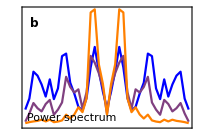

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

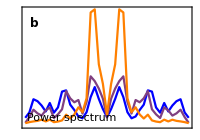

```mathematica
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAc1,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc1,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

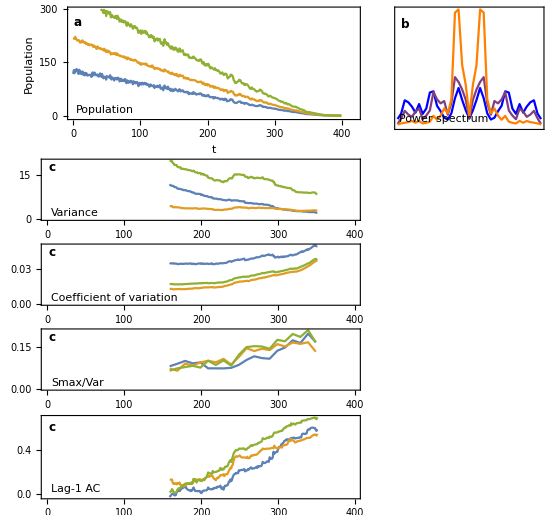

```mathematica
plotGrid
```

```mathematica
Export["figures/singles_"<>simName<>".png",plotGrid,ImageResolution->200];
```